## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
Needs["Toolbox`"];
Get["MASSFittingPackage`"];
Get["MASSFittingPackage`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="G3PD2";
KeqEquilibrator=2.4*10^-5;

pathMASSFittingPath = "/home/mrama/Dropbox/MASS_fitting_package/";

mainFolder = "test_refactor";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPath,mainFolder];
```

/home/mrama/Dropbox/MASS_fitting_package/data

Working dir:/home/mrama/Dropbox/MASS_fitting_package/examples/

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data.csv"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.csv"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.csv"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

### Print Module Dependent Information

```mathematica
printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Km Values:

Substrate | Km_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
nadph | 3.4×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
dhap | 0.00018 |  | M | 7.4 | 23 | trishcl | 0.1 | 
nadp | 0.000165 |  | M | 7.4 | 23 | trishcl | 0.1 | 
glyc3p | 0.00003 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Substrate | S0.5_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Metabolite(s) | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Parameter_Type | Inhibitor | Value | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Kic | glyc3p | 4.2×10^-6 | nadph | 0.0001 | Competitive | Null | Null | dhap | Null | M | 7.4 | 23 | trishcl | 0.1 | 
Kincu | glyc3p | 6.5×10^-6 | dhap | 0.0001 | NonCompetitive | Null | Null | nadph | Null | M | 7.4 | 23 | trishcl | 0.1 | 
Kincc | glyc3p | 2.5×10^-6 | dhap | 0.0001 | NonCompetitive | Null | Null | nadph | Null | M | 7.4 | 23 | trishcl | 0.1 | 
Kincu | nadp | 0.0013 | nadph | 0.00001 | NonCompetitive | Null | Null | dhap | Null | M | 7.4 | 23 | trishcl | 0.1 | 
Kincc | nadp | 0.0013 | nadph | 0.00001 | NonCompetitive | Null | Null | dhap | Null | M | 7.4 | 23 | trishcl | 0.1 | 
Kic | nadp | 0.000187 | dhap | 0.002 | Competitive | Null | Null | nadph | Null | M | 7.4 | 23 | trishcl | 0.1 | 
Kic | dhap | 0.000038 | nadp | 0.002 | Competitive | Null | Null | glyc3p | Null | M | 7.4 | 23 | trishcl | 0.1 | 
Kincu | dhap | 0.00024 | glyc3p | 0.0001 | NonCompetitive | Null | Null | nadp | Null | M | 7.4 | 23 | trishcl | 0.1 | 
Kincc | dhap | 0.00012 | glyc3p | 0.0001 | NonCompetitive | Null | Null | nadp | Null | M | 7.4 | 23 | trishcl | 0.1 | 
Kincu | nadph | 8.×10^-7 | nadp | 0.0001 | NonCompetitive | Null | Null | glyc3p | Null | M | 7.4 | 23 | trishcl | 0.1 | 
Kincc | nadph | 6.×10^-7 | nadp | 0.0001 | NonCompetitive | Null | Null | glyc3p | Null | M | 7.4 | 23 | trishcl | 0.1 | 
Kic | nadph | 4.×10^-7 | glyc3p | 0.0002 | Competitive | Null | Null | nadp | Null | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Parameter_Type | Activator | Value | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Parameter_Type | Metabolite | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Construct enzyme module

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

```mathematica
{{"ordered bi bi"}, {"\"[nadp,glyc3p,dhap,nadph]\""}}
```

```mathematica
catalyticBranch={"E_G3PD2[c] + nadp[c] <=> E_G3PD2[c]&nadp",
				"E_G3PD2[c]&nadp + glyc3p[c] <=> E_G3PD2[c]&nadp&glyc3p",
				"E_G3PD2[c]&nadp&glyc3p <=> E_G3PD2[c]&nadph&dhap",
				"E_G3PD2[c]&nadph&dhap <=> E_G3PD2[c]&nadph + dhap[c]",
				"E_G3PD2[c]&nadph <=> E_G3PD2[c] + nadph[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites-> 0];
```

### Setup King-Altmann Equations

```mathematica
rxnMets =  Map[getID[#]&, Flatten[{getSubstrates[rxn], getProducts[rxn]}]];
inhibitors =inhibitionList[[All,2]] ;
prodInhibBool = MemberQ[Map[MemberQ[rxnMets, #]&, inhibitors], True];

{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={{"prod_inhib_dhap", nadph^c->0},{"prod_inhib_nadph", dhap^c->0}};
otherMetsForwardZeroSub={{"prod_inhib_glyc3p", nadp^c->0},{"prod_inhib_nadp", glyc3p^c->0}};

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;
simplifyMaxTime=1*^-5;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
eqRateConstSub={};


(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)

absoluteFluxNoProdInhib=
	If[prodInhibBool,
		getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs, "NoProdInhibRefactor"],
		Null
	];


{enzymeModel, nonCatalyticReactions} =addInhibitionReactions[enzymeModel, rxnName, inhibitionList[[{2,3,8,9}]],  allCatalyticReactions, nonCatalyticReactions];
nonCatalyticReactions//TableForm
```

((G3PD2^c&nadph^c)_^+glyc3p^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_Kincu_glyc3p_1_nadph
((G3PD2^c)_^+glyc3p^c⇌(G3PD2^c&glyc3p^c)_^)^G3PD2_Kincc_glyc3p_1_nadph
((G3PD2^c&glyc3p^c)_^+nadph^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_NC_glyc3p
((G3PD2^c&nadp^c)_^+dhap^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_Kincu_dhap_1_nadp
((G3PD2^c)_^+dhap^c⇌(G3PD2^c&dhap^c)_^)^G3PD2_Kincc_dhap_1_nadp
((G3PD2^c&dhap^c)_^+nadp^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_NC_dhap

```mathematica
(* get flux equation including inhibitions*)
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs];

(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getRateConstSubRandomMech[enzymeModel, eqRateConstSub, allCatalyticReactions, nonCatalyticReactions, competitiveRxns];
eqRateConstSub={};

{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub, absoluteFluxNoProdInhib, absoluteFluxNoProdInhib,
otherMetsForwardZeroSub, otherMetsReverseZeroSub];

(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal,
															otherAbsoluteRatesForward, otherAbsoluteRatesReverse];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub, otherAbsoluteRatesForward, otherAbsoluteRatesReverse];
```

## Semi-Automated Simulate Data

### User Input Section

```mathematica
logStepSize=0.2;
(*nonKmParamWeight=3;*)
(*Weighting factor for non-Km data points. You can be specify this manually*)
{minPsDataVal, maxPsDataVal}= getMinMaxPsDataVal[1];
nonKmParamWeight=Length[Table[1,{i,minPsDataVal, maxPsDataVal,logStepSize}]];
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)
```

### Simulate data

```mathematica
pHandT={7.4,23};
kmFittingData= simulateKmData[rxn, metsFull,  metSatForSub, metSatRevSub, kmList, otherParmsList, assumedSaturatingConc, eTotal,
			   logStepSize,activeIsoSub, bufferInfo, ionCharge,  inputPath, fileList, KeqEquilibrator];

haldane=haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
haldaneRatio=haldane[[2]];

{KeqFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[haldaneRatio,KeqEquilibrator, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT,"haldaneRatio"];

logStepSize=0.5;
inhibFittingData=simulateInhibData[rxn, metsFull, metSatForSub, metSatRevSub,  inhibitionList, kmList, assumedSaturatingConc, eTotal,
			   logStepSize, activeIsoSub, bufferInfo, ionCharge, inputPath, fileList, KeqEquilibrator];
```

### Sanity check plots

#### C inhib of dhap by glyc3p

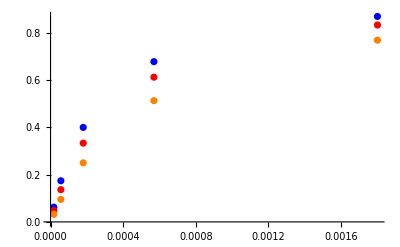

```mathematica
inhib1=inhibFittingData[[1;;5,{2,-1}]];
inhib2=inhibFittingData[[6;;10,{2,-1}]];
inhib3=inhibFittingData[[11;;15,{2,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.00027}

{1.,0.00036}

{1.,0.00054}

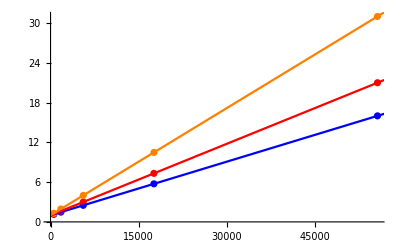

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,0,100000}, PlotStyle->{Blue,Red, Orange}]]
```

#### NC inhib of nadph by glyc3p

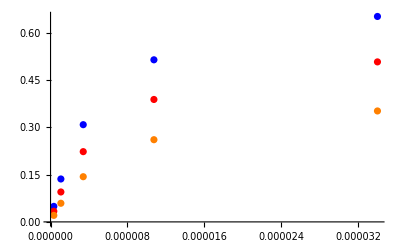

```mathematica
inhib1=inhibFittingData[[16;;20,{5,-1}]];
inhib2=inhibFittingData[[21;;25,{5,-1}]];
inhib3=inhibFittingData[[26;;30,{5,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.34615,6.46×10^-6}

{1.69231,9.52×10^-6}

{2.38462,0.00001564}

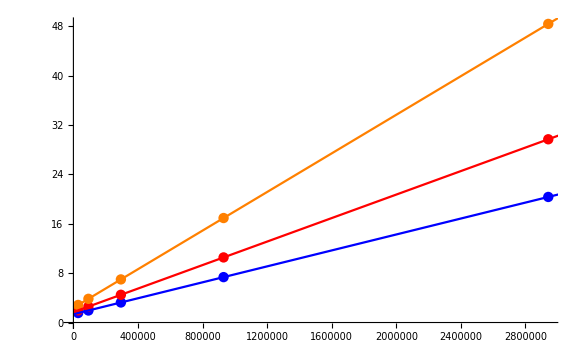

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### NC inhib of dhap by nadp

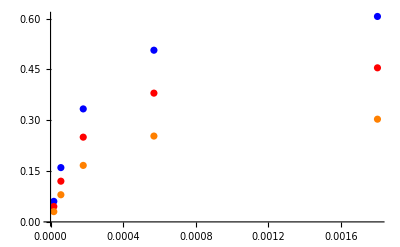

```mathematica
inhib1=inhibFittingData[[31;;35,{2,-1}]];
inhib2=inhibFittingData[[36;;40,{2,-1}]];
inhib3=inhibFittingData[[41;;45,{2,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.5,0.00027}

{2.,0.00036}

{3.,0.00054}

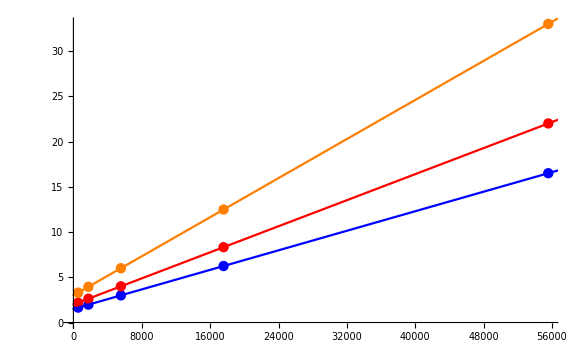

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### C inhib of nadph by nadp

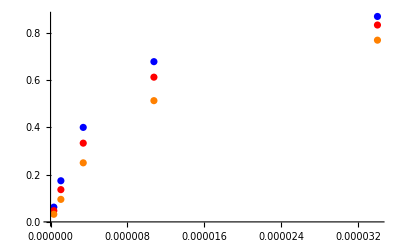

```mathematica
inhib1=inhibFittingData[[46;;50,{5,-1}]];
inhib2=inhibFittingData[[51;;55,{5,-1}]];
inhib3=inhibFittingData[[56;;60,{5,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,5.1×10^-6}

{1.,6.8×10^-6}

{1.,0.0000102}

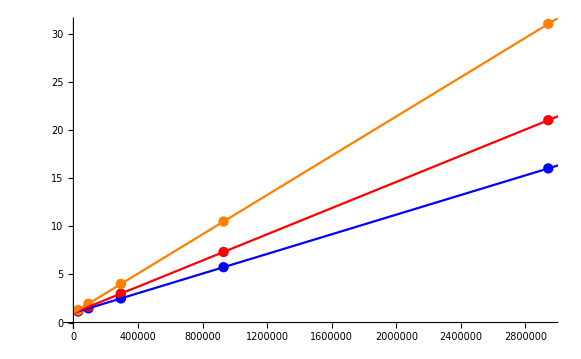

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### C inhib of glyc3p by dhap

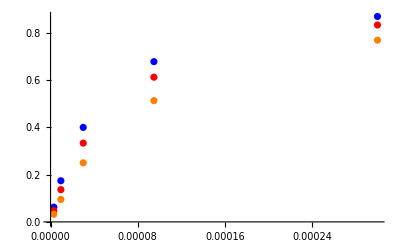

```mathematica
inhib1=inhibFittingData[[61;;65,{3,-1}]];
inhib2=inhibFittingData[[66;;70,{3,-1}]];
inhib3=inhibFittingData[[71;;75,{3,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.000045}

{1.,0.00006}

{1.,0.00009}

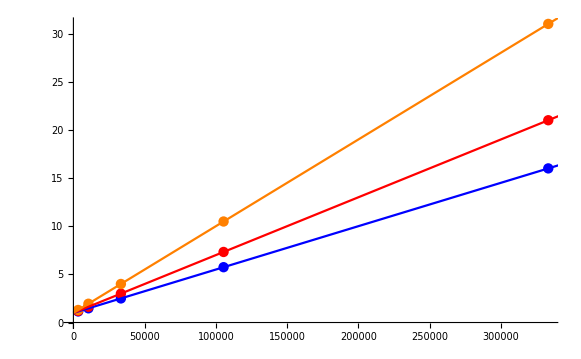

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### NC inhib of nadp by dhap

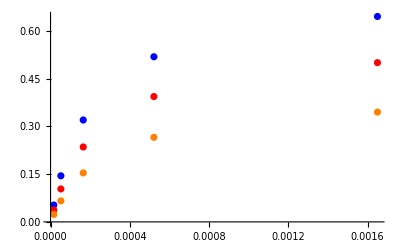

```mathematica
inhib1=inhibFittingData[[76;;80,{4,-1}]];
inhib2=inhibFittingData[[81;;85,{4,-1}]];
inhib3=inhibFittingData[[86;;90,{4,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.375,0.00028875}

{1.75,0.0004125}

{2.5,0.00066}

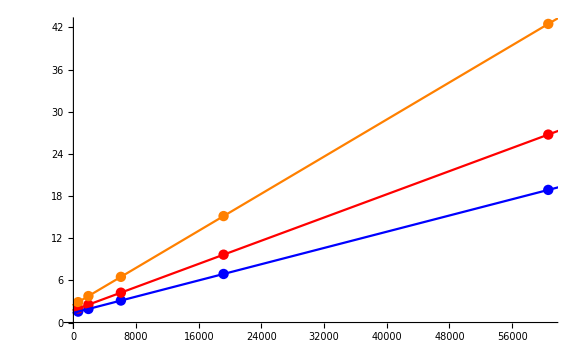

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### C inhib of nadp by nadph

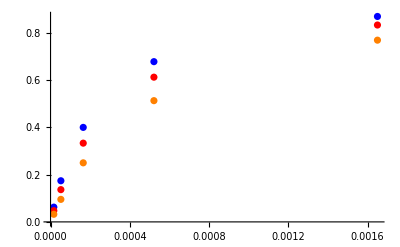

```mathematica
inhib1=inhibFittingData[[106;;110,{4,-1}]];
inhib2=inhibFittingData[[111;;115,{4,-1}]];
inhib3=inhibFittingData[[116;;120,{4,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.0002475}

{1.,0.00033}

{1.,0.000495}

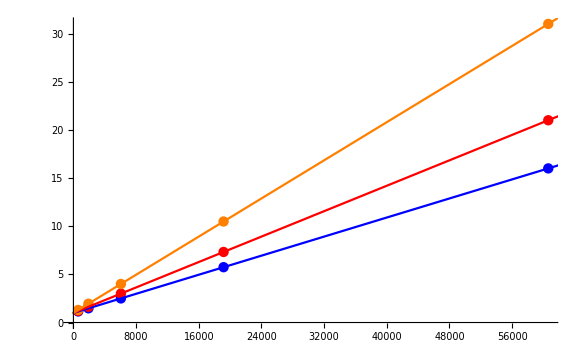

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

```mathematica
rxn
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

### Assemble and export All Data

```mathematica
header=Join[Map[ToString, metsSub[[All,1]]],{"FileFlag", "Target_Data"}];
fittingData = Flatten[{kmFittingData,KeqFittingData,inhibFittingData}, 1];

dataPath =FileNameJoin[{inputPath,rxnName <>".dat"}, OperatingSystem->$OperatingSystem];

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
FilePrint[dataPath];
```

Keq_G3PD2	dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	param_E_total	param_pH	param_Temp	FileFlag	Target_Data
0.000024	0.01	0	0	3.400000000000002e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_nadph.txt	0.09090909090909097
0.000024	0.01	0	0	5.388636854367791e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_nadph.txt	0.1368068886032101
0.000024	0.01	0	0	8.540413867132584e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_nadph.txt	0.20076000891310194
0.000024	0.01	0	0	1.3535643798818904e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_nadph.txt	0.2847472489508014
0.000024	0.01	0	0	2.1452549712326573e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_nadph.txt	0.386863179846857
0.000024	0.01	0	0	3.4000000000000018e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_nadph.txt	0.5000000000000001
0.000024	0.01	0	0	5.388636854367791e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_nadph.txt	0.6131368201531433
0.000024	0.01	0	0	8.540413867132584e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_nadph.txt	0.7152527510491989
0.000024	0.01	0	0	0.000013535643798818902	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_nadph.txt	0.7992399910868982
0.000024	0.01	0	0	0.000021452549712326573	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_nadph.txt	0.86319311139679
0.000024	0.01	0	0	0.00003400000000000002	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_nadph.txt	0.9090909090909091
0.000024	0.000018000000000000017	0	0	0.01	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_dhap.txt	0.09090909090909098
0.000024	0.00002852807746430008	0	0	0.01	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_dhap.txt	0.13680688860321016
0.000024	0.00004521395576717252	0	0	0.01	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_dhap.txt	0.200760008913102
0.000024	0.00007165929069962952	0	0	0.01	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_dhap.txt	0.28474724895080145
0.000024	0.00011357232200643484	0	0	0.01	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_dhap.txt	0.38686317984685703
0.000024	0.00018000000000000017	0	0	0.01	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_dhap.txt	0.5000000000000002
0.000024	0.0002852807746430008	0	0	0.01	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_dhap.txt	0.6131368201531433
0.000024	0.0004521395576717252	0	0	0.01	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_dhap.txt	0.7152527510491989
0.000024	0.0007165929069962958	0	0	0.01	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_dhap.txt	0.7992399910868984
0.000024	0.0011357232200643484	0	0	0.01	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_dhap.txt	0.86319311139679
0.000024	0.0018000000000000017	0	0	0.01	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateRev_dhap.txt	0.9090909090909092
0.000024	0	0.01	0.000016500000000000015	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_nadp.txt	0.09090909090909097
0.000024	0	0.01	0.000026150737675608408	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_nadp.txt	0.13680688860321016
0.000024	0	0.01	0.000041446126119908146	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_nadp.txt	0.20076000891310203
0.000024	0	0.01	0.00006568768314132706	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_nadp.txt	0.2847472489508014
0.000024	0	0.01	0.00010410796183923194	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_nadp.txt	0.3868631798468571
0.000024	0	0.01	0.00016500000000000016	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_nadp.txt	0.5000000000000002
0.000024	0	0.01	0.0002615073767560841	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_nadp.txt	0.6131368201531434
0.000024	0	0.01	0.0004144612611990815	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_nadp.txt	0.7152527510491989
0.000024	0	0.01	0.0006568768314132713	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_nadp.txt	0.7992399910868985
0.000024	0	0.01	0.0010410796183923194	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_nadp.txt	0.8631931113967901
0.000024	0	0.01	0.0016500000000000017	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_nadp.txt	0.9090909090909092
0.000024	0	3.0000000000000013e-6	0.01	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_glyc3p.txt	0.09090909090909094
0.000024	0	4.7546795773833446e-6	0.01	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_glyc3p.txt	0.1368068886032101
0.000024	0	7.535659294528749e-6	0.01	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_glyc3p.txt	0.20076000891310194
0.000024	0	0.000011943215116604912	0.01	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_glyc3p.txt	0.28474724895080133
0.000024	0	0.000018928720334405797	0.01	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_glyc3p.txt	0.3868631798468569
0.000024	0	0.00003000000000000001	0.01	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_glyc3p.txt	0.5000000000000001
0.000024	0	0.00004754679577383344	0.01	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_glyc3p.txt	0.6131368201531432
0.000024	0	0.00007535659294528749	0.01	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_glyc3p.txt	0.7152527510491988
0.000024	0	0.00011943215116604925	0.01	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_glyc3p.txt	0.7992399910868984
0.000024	0	0.00018928720334405796	0.01	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_glyc3p.txt	0.86319311139679
0.000024	0	0.00030000000000000014	0.01	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/relRateFor_glyc3p.txt	0.9090909090909091
0.000024	0	0	0	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/haldaneRatio.txt	0.000024
0.000024	0	0	0	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/haldaneRatio.txt	0.000024
0.000024	0	0	0	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/haldaneRatio.txt	0.000024
0.000024	0	0	0	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/haldaneRatio.txt	0.000024
0.000024	0	0	0	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/haldaneRatio.txt	0.000024
0.000024	0	0	0	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/haldaneRatio.txt	0.000024
0.000024	0	0	0	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/haldaneRatio.txt	0.000024
0.000024	0	0	0	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/haldaneRatio.txt	0.000024
0.000024	0	0	0	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/haldaneRatio.txt	0.000024
0.000024	0	0	0	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/haldaneRatio.txt	0.000024
0.000024	0	0	0	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/haldaneRatio.txt	0.000024
0.000024	0.000018000000000000017	2.1e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.06250000000000006
0.000024	0.000056920997883030876	2.1e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.17411239489546845
0.000024	0.00018000000000000017	2.1e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.4000000000000002
0.000024	0.0005692099788303088	2.1e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.6782688399674107
0.000024	0.0018000000000000017	2.1e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.8695652173913044
0.000024	0.000018000000000000017	4.2e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.047619047619047665
0.000024	0.000056920997883030876	4.2e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.13652705949581442
0.000024	0.00018000000000000017	4.2e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.33333333333333354
0.000024	0.0005692099788303088	4.2e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.6125741132772071
0.000024	0.0018000000000000017	4.2e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.8333333333333335
0.000024	0.000018000000000000017	8.4e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.032258064516129066
0.000024	0.000056920997883030876	8.4e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.09535767393826004
0.000024	0.00018000000000000017	8.4e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.2500000000000002
0.000024	0.0005692099788303088	8.4e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.5131670194948622
0.000024	0.0018000000000000017	8.4e-6	0	0.0001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.7692307692307694
0.000024	0.0001	2.25e-6	0	3.400000000000002e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.04914933837429115
0.000024	0.0001	2.25e-6	0	1.0751744044572496e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.1359715179829786
0.000024	0.0001	2.25e-6	0	3.4000000000000018e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.3080568720379148
0.000024	0.0001	2.25e-6	0	0.000010751744044572496	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.5136142175737065
0.000024	0.0001	2.25e-6	0	0.00003400000000000002	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.6509764646970455
0.000024	0.0001	4.5e-6	0	3.400000000000002e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.03367875647668395
0.000024	0.0001	4.5e-6	0	1.0751744044572496e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.09481652165128764
0.000024	0.0001	4.5e-6	0	3.4000000000000018e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.22260273972602748
0.000024	0.0001	4.5e-6	0	0.000010751744044572496	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.3879359014999326
0.000024	0.0001	4.5e-6	0	0.00003400000000000002	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.5070202808112324
0.000024	0.0001	9.e-6	0	3.400000000000002e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.0206677265500795
0.000024	0.0001	9.e-6	0	1.0751744044572496e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.059062933642962216
0.000024	0.0001	9.e-6	0	3.4000000000000018e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.14317180616740097
0.000024	0.0001	9.e-6	0	0.000010751744044572496	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.2604666499256048
0.000024	0.0001	9.e-6	0	0.00003400000000000002	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_glyc3p.txt	0.351541373715522
0.000024	0.000018000000000000017	0	0.00065	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.06060606060606066
0.000024	0.000056920997883030876	0	0.00065	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.16016871556802817
0.000024	0.00018000000000000017	0	0.00065	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.3333333333333335
0.000024	0.0005692099788303088	0	0.00065	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.5064979510986386
0.000024	0.0018000000000000017	0	0.00065	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.6060606060606061
0.000024	0.000018000000000000017	0	0.0013	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.04545454545454549
0.000024	0.000056920997883030876	0	0.0013	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.12012653667602116
0.000024	0.00018000000000000017	0	0.0013	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.2500000000000001
0.000024	0.0005692099788303088	0	0.0013	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.379873463323979
0.000024	0.0018000000000000017	0	0.0013	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.4545454545454546
0.000024	0.000018000000000000017	0	0.0026	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.03030303030303033
0.000024	0.000056920997883030876	0	0.0026	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.08008435778401408
0.000024	0.00018000000000000017	0	0.0026	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.16666666666666674
0.000024	0.0005692099788303088	0	0.0026	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.2532489755493193
0.000024	0.0018000000000000017	0	0.0026	0.00001	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.30303030303030304
0.000024	0.002	0	0.0000935	3.400000000000002e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.06250000000000003
0.000024	0.002	0	0.0000935	1.0751744044572496e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.1741123948954684
0.000024	0.002	0	0.0000935	3.4000000000000018e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.40000000000000013
0.000024	0.002	0	0.0000935	0.000010751744044572496	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.6782688399674105
0.000024	0.002	0	0.0000935	0.00003400000000000002	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.8695652173913044
0.000024	0.002	0	0.000187	3.400000000000002e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.047619047619047644
0.000024	0.002	0	0.000187	1.0751744044572496e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.1365270594958144
0.000024	0.002	0	0.000187	3.4000000000000018e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.3333333333333334
0.000024	0.002	0	0.000187	0.000010751744044572496	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.612574113277207
0.000024	0.002	0	0.000187	0.00003400000000000002	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.8333333333333334
0.000024	0.002	0	0.000374	3.400000000000002e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.032258064516129045
0.000024	0.002	0	0.000374	1.0751744044572496e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.09535767393826002
0.000024	0.002	0	0.000374	3.4000000000000018e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.2500000000000001
0.000024	0.002	0	0.000374	0.000010751744044572496	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.5131670194948621
0.000024	0.002	0	0.000374	0.00003400000000000002	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadp.txt	0.7692307692307694
0.000024	0.000019	3.0000000000000013e-6	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.06250000000000003
0.000024	0.000019	9.486832980505141e-6	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.17411239489546837
0.000024	0.000019	0.00003000000000000001	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.40000000000000013
0.000024	0.000019	0.00009486832980505142	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.6782688399674105
0.000024	0.000019	0.00030000000000000014	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.8695652173913044
0.000024	0.000038	3.0000000000000013e-6	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.04761904761904764
0.000024	0.000038	9.486832980505141e-6	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.13652705949581434
0.000024	0.000038	0.00003000000000000001	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.3333333333333334
0.000024	0.000038	0.00009486832980505142	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.612574113277207
0.000024	0.000038	0.00030000000000000014	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.8333333333333335
0.000024	0.000076	3.0000000000000013e-6	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.032258064516129045
0.000024	0.000076	9.486832980505141e-6	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.09535767393826
0.000024	0.000076	0.00003000000000000001	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.25000000000000006
0.000024	0.000076	0.00009486832980505142	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.5131670194948622
0.000024	0.000076	0.00030000000000000014	0.002	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.7692307692307693
0.000024	0.00009	0.0001	0.000016500000000000015	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.052980132450331174
0.000024	0.00009	0.0001	0.000052177581392778313	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.1447390418373348
0.000024	0.00009	0.0001	0.00016500000000000016	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.3200000000000002
0.000024	0.00009	0.0001	0.0005217758139277831	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.518564992170751
0.000024	0.00009	0.0001	0.0016500000000000017	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.6451612903225806
0.000024	0.00018	0.0001	0.000016500000000000015	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.03738317757009349
0.000024	0.00018	0.0001	0.000052177581392778313	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.10356583218373844
0.000024	0.00018	0.0001	0.00016500000000000016	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.235294117647059
0.000024	0.00018	0.0001	0.0005217758139277831	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.39361254767503817
0.000024	0.00018	0.0001	0.0016500000000000017	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.5000000000000001
0.000024	0.00036	0.0001	0.000016500000000000015	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.023529411764705903
0.000024	0.00036	0.0001	0.000052177581392778313	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.06601047571169773
0.000024	0.00036	0.0001	0.00016500000000000016	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.1538461538461539
0.000024	0.00036	0.0001	0.0005217758139277831	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.26561052385648354
0.000024	0.00036	0.0001	0.0016500000000000017	0	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_dhap.txt	0.3448275862068966
0.000024	0	3.0000000000000013e-6	0.0001	3.5e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.057901085645355864
0.000024	0	9.486832980505141e-6	0.0001	3.5e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.15517252975139625
0.000024	0	0.00003000000000000001	0.0001	3.5e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.33103448275862074
0.000024	0	0.00009486832980505142	0.0001	3.5e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.5159442342521813
0.000024	0	0.00030000000000000014	0.0001	3.5e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.6266318537859008
0.000024	0	3.0000000000000013e-6	0.0001	7.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.042477876106194704
0.000024	0	9.486832980505141e-6	0.0001	7.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.11459214550830052
0.000024	0	0.00003000000000000001	0.0001	7.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.2474226804123712
0.000024	0	0.00009486832980505142	0.0001	7.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.39060056309756436
0.000024	0	0.00030000000000000014	0.0001	7.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.47808764940239046
0.000024	0	3.0000000000000013e-6	0.0001	1.4e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.02771362586605082
0.000024	0	9.486832980505141e-6	0.0001	1.4e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.07523930500173176
0.000024	0	0.00003000000000000001	0.0001	1.4e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.16438356164383564
0.000024	0	0.00009486832980505142	0.0001	1.4e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.2628747818212248
0.000024	0	0.00030000000000000014	0.0001	1.4e-6	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.32432432432432434
0.000024	0	0.0002	0.000016500000000000015	2.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.06250000000000006
0.000024	0	0.0002	0.000052177581392778313	2.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.17411239489546848
0.000024	0	0.0002	0.00016500000000000016	2.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.4000000000000002
0.000024	0	0.0002	0.0005217758139277831	2.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.6782688399674106
0.000024	0	0.0002	0.0016500000000000017	2.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.8695652173913045
0.000024	0	0.0002	0.000016500000000000015	4.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.047619047619047665
0.000024	0	0.0002	0.000052177581392778313	4.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.13652705949581445
0.000024	0	0.0002	0.00016500000000000016	4.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.33333333333333354
0.000024	0	0.0002	0.0005217758139277831	4.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.6125741132772071
0.000024	0	0.0002	0.0016500000000000017	4.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.8333333333333335
0.000024	0	0.0002	0.000016500000000000015	8.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.03225806451612906
0.000024	0	0.0002	0.000052177581392778313	8.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.09535767393826007
0.000024	0	0.0002	0.00016500000000000016	8.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.25000000000000017
0.000024	0	0.0002	0.0005217758139277831	8.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.5131670194948623
0.000024	0	0.0002	0.0016500000000000017	8.e-7	1	7.4	23	/home/mrama/Dropbox/MASS_fitting_package/examples/test_refactor/input/prod_inhib_nadph.txt	0.7692307692307693

## Configure the Particle Swarm Optimization

```mathematica
numTrials=5;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, dataPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateFor.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/absRateRev.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_g3p.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_nad.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateFor_pi.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateRev_13dpg.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/relRateRev_nadh.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/haldaneRatio.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/KdRatio.txt,/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/dKdRatio.txt]
data_file_name	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/input/GAPD.dat
value_row	-1
function_row	-2
data_row_high	-2
summary_file_name	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/output/raw/summary.txt
ultimate_result_name	/home/mrama/Dropbox/MASS_fitting_package/examples/fit_dKd/output/raw/psoResults.txt

## Configure the Levenberg-Marquardt Algorithm

```mathematica
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, dataPath, finalRateConsts, fileList, lowerParamBound, upperParamBound];
```

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	22
candidates_import_path	/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/output/raw/psoResults.txt
candidates_export_path	/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/output/raw/lmaResults.txt
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/input/absRateFor.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/input/absRateRev.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/input/relRateFor_glyc3p.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/input/relRateFor_nadp.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/input/relRateRev_dhap.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/input/relRateRev_nadph.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/input/prod_inhib_dhap.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/input/prod_inhib_nadph.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/input/prod_inhib_glyc3p.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/input/prod_inhib_nadp.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/input/haldaneRatio.txt]
data_file_name	/home/mrama/Dropbox/Kinetics/Enzymes_new/G3PD2/test_refactor/input/G3PD2.dat
value_row	-1
function_row	-2
data_row_high	-2

### Make the shell script to run pso and lma fitting methods

```mathematica
runFitScriptPath="/home/mrama/Dropbox/Kinetics/Scripts/run_fit_rel.py"
shRunFit=createCombinedFitShellScript[runFitScriptPath, psoParameterPath, lmaParameterPath, psoTrialSummaryFileName, psoResultsFileName, lmaResultsFileName, numTrials, dataPath];

shRunFitPath=inputPath<>"runFit.sh";
Export[shRunFitPath,shRunFit,"Table"];

(*Make the Shell Script Executable*)
mkShRunFitExec="chmod u+x "<> shRunFitPath;
mkShRunFitExecCmd="!"<>mkShRunFitExec<>" 2>&1";
Import[mkShRunFitExecCmd,"Text"];
```

/home/mrama/Dropbox/Kinetics/Scripts/run_fit_rel.py

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runBothCmd="cd "<>inputPath<>" && ./"<>"runFit.sh";
runBothExe="!"<>runBothCmd<>" 2>&1";
Import[runBothExe,"Text"]
```

best_fit: 5.20214971656
best_fit: 11.3530198528
best_fit: 8.03050813666
best_fit: 2.71457695991
best_fit: 10.3974864859

#### Run the PSO Algorithm Independently - not working

```mathematica
runShRunPsoExec="cd "<>outputPath<>" && ./"<>"runPso.sh"

(*You can copy+paste this output to a shell*)
```

cd /home/mrama/Dropbox/Kinetics/Enzymes_new/GAPD_dKd/Parameter_Fitting/Development/ && ./runPso.sh

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runShRunPsoCmd="!"<>runShRunPsoExec<>" 2>&1";
Import[runShRunPsoCmd,"Text"]
```

#### Run the Levenberg-Marquardt Algorithm Independently - not working

The Levenberg-Marquardt Algorithm needs to be run after the Particle Swarm Optimization

```mathematica
lmaRunCmd="python "<>lmaScriptPath<>" "<>lmaParameterPath<>" "<>psoResultsFileName<>" "<>resultsFileName

(*You can copy+paste this output to a shell*)
```

python /media/users/jdebree/ProjectFiles/Scripts/lma_ver0.10.1.py /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaParameters.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/psoResults.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaResults.txt

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
lmaRunExe="!"<>lmaRunCmd<>" 2>&1";
Import[lmaRunExe,"Text"]
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
fittingData = Import[inputPath <> "G3PD2.dat"];
fittingData = fittingData[[2;;,All]];
resultsFile = "raw/lmaResults.txt";
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,""];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Relative error | True value | Predicted Value
 |  |  | 
prod_inhib_glyc3p | 52.0945 | 0.0625 | 0.0950591
prod_inhib_glyc3p | 40.4472 | 0.174112 | 0.244536
prod_inhib_glyc3p | 21.526 | 0.4 | 0.486104
prod_inhib_glyc3p | 3.9343 | 0.678269 | 0.704954
prod_inhib_glyc3p | 6.44477 | 0.869565 | 0.813524
prod_inhib_glyc3p | 74.6298 | 0.047619 | 0.083157
prod_inhib_glyc3p | 60.4322 | 0.136527 | 0.219033
prod_inhib_glyc3p | 35.8854 | 0.333333 | 0.452951
prod_inhib_glyc3p | 11.3432 | 0.612574 | 0.68206
prod_inhib_glyc3p | 3.55861 | 0.833333 | 0.803678
prod_inhib_glyc3p | 106.161 | 0.0322581 | 0.0665036
prod_inhib_glyc3p | 90.0551 | 0.0953577 | 0.181232
prod_inhib_glyc3p | 59.4337 | 0.25 | 0.398584
prod_inhib_glyc3p | 24.8053 | 0.513167 | 0.64046
prod_inhib_glyc3p | 2.00907 | 0.769231 | 0.784685
prod_inhib_glyc3p | 17.3592 | 0.0491493 | 0.0406174
prod_inhib_glyc3p | 23.9328 | 0.135972 | 0.10343
prod_inhib_glyc3p | 34.2924 | 0.308057 | 0.202417
prod_inhib_glyc3p | 43.486 | 0.513614 | 0.290264
prod_inhib_glyc3p | 48.3182 | 0.650976 | 0.336436
prod_inhib_glyc3p | 19.1964 | 0.0336788 | 0.0401439
prod_inhib_glyc3p | 5.90321 | 0.0948165 | 0.100414
prod_inhib_glyc3p | 14.1163 | 0.222603 | 0.19118
prod_inhib_glyc3p | 30.9937 | 0.387936 | 0.2677
prod_inhib_glyc3p | 39.5501 | 0.50702 | 0.306493
prod_inhib_glyc3p | 89.8089 | 0.0206677 | 0.0392292
prod_inhib_glyc3p | 60.643 | 0.0590629 | 0.0948805
prod_inhib_glyc3p | 20.1871 | 0.143172 | 0.172074
prod_inhib_glyc3p | 11.0517 | 0.260467 | 0.231681
prod_inhib_glyc3p | 25.9885 | 0.351541 | 0.260181
prod_inhib_nadp | 3.47733 | 0.0606061 | 0.0584986
prod_inhib_nadp | 5.05829 | 0.160169 | 0.152067
prod_inhib_nadp | 8.04581 | 0.333333 | 0.306514
prod_inhib_nadp | 12.4321 | 0.506498 | 0.44353
prod_inhib_nadp | 19.9952 | 0.606061 | 0.484877
prod_inhib_nadp | 8.6714 | 0.0454545 | 0.041513
prod_inhib_nadp | 5.44075 | 0.120127 | 0.113591
prod_inhib_nadp | 0.4384 | 0.25 | 0.251096
prod_inhib_nadp | 5.38268 | 0.379873 | 0.400321
prod_inhib_nadp | 2.0884 | 0.454545 | 0.464038
prod_inhib_nadp | 13.335 | 0.030303 | 0.0262621
prod_inhib_nadp | 5.82014 | 0.0800844 | 0.0754233
prod_inhib_nadp | 10.6473 | 0.166667 | 0.184412
prod_inhib_nadp | 32.2972 | 0.253249 | 0.335041
prod_inhib_nadp | 41.0117 | 0.30303 | 0.427308
prod_inhib_nadp | 40.3696 | 0.0625 | 0.037269
prod_inhib_nadp | 37.9254 | 0.174112 | 0.10808
prod_inhib_nadp | 32.3103 | 0.4 | 0.270759
prod_inhib_nadp | 23.8213 | 0.678269 | 0.516696
prod_inhib_nadp | 16.6341 | 0.869565 | 0.724921
prod_inhib_nadp | 22.7779 | 0.047619 | 0.0367724
prod_inhib_nadp | 21.805 | 0.136527 | 0.106757
prod_inhib_nadp | 19.5615 | 0.333333 | 0.268128
prod_inhib_nadp | 16.1481 | 0.612574 | 0.513655
prod_inhib_nadp | 13.2374 | 0.833333 | 0.723022
prod_inhib_nadp | 11.0355 | 0.0322581 | 0.0358179
prod_inhib_nadp | 9.28103 | 0.0953577 | 0.104208
prod_inhib_nadp | 5.20699 | 0.25 | 0.263017
prod_inhib_nadp | 1.06946 | 0.513167 | 0.507679
prod_inhib_nadp | 6.4971 | 0.769231 | 0.719253
prod_inhib_dhap | 16.055 | 0.0625 | 0.0524656
prod_inhib_dhap | 11.0709 | 0.174112 | 0.154837
prod_inhib_dhap | 0.669142 | 0.4 | 0.397323
prod_inhib_dhap | 4.73469 | 0.678269 | 0.710383
prod_inhib_dhap | 22.875 | 0.869565 | 0.670652
prod_inhib_dhap | 6.76662 | 0.047619 | 0.0508412
prod_inhib_dhap | 10.0636 | 0.136527 | 0.150267
prod_inhib_dhap | 16.1534 | 0.333333 | 0.387178
prod_inhib_dhap | 13.9675 | 0.612574 | 0.698136
prod_inhib_dhap | 20.1455 | 0.833333 | 0.665454
prod_inhib_dhap | 48.3384 | 0.0322581 | 0.0478511
prod_inhib_dhap | 48.7243 | 0.0953577 | 0.14182
prod_inhib_dhap | 47.2858 | 0.25 | 0.368215
prod_inhib_dhap | 31.4787 | 0.513167 | 0.674705
prod_inhib_dhap | 14.8179 | 0.769231 | 0.655247
prod_inhib_dhap | 51.0433 | 0.0529801 | 0.080023
prod_inhib_dhap | 40.9897 | 0.144739 | 0.204067
prod_inhib_dhap | 25.0869 | 0.32 | 0.400278
prod_inhib_dhap | 10.9132 | 0.518565 | 0.575157
prod_inhib_dhap | 3.44038 | 0.645161 | 0.667357
prod_inhib_dhap | 20.2507 | 0.0373832 | 0.0449535
prod_inhib_dhap | 20.5873 | 0.103566 | 0.124887
prod_inhib_dhap | 21.2629 | 0.235294 | 0.285325
prod_inhib_dhap | 22.085 | 0.393613 | 0.480542
prod_inhib_dhap | 22.6437 | 0.5 | 0.613219
prod_inhib_dhap | 0.354163 | 0.0235294 | 0.0234461
prod_inhib_dhap | 4.41757 | 0.0660105 | 0.0689265
prod_inhib_dhap | 15.8924 | 0.153846 | 0.178296
prod_inhib_dhap | 34.7323 | 0.265611 | 0.357863
prod_inhib_dhap | 52.2782 | 0.344828 | 0.525097
prod_inhib_nadph | 47.6586 | 0.0579011 | 0.0303062
prod_inhib_nadph | 44.9009 | 0.155173 | 0.0854986
prod_inhib_nadph | 39.6284 | 0.331034 | 0.199851
prod_inhib_nadph | 35.9221 | 0.515944 | 0.330606
prod_inhib_nadph | 43.6736 | 0.626632 | 0.352959
prod_inhib_nadph | 39.1148 | 0.0424779 | 0.0258627
prod_inhib_nadph | 39.0738 | 0.114592 | 0.0698166
prod_inhib_nadph | 39.3955 | 0.247423 | 0.149949
prod_inhib_nadph | 41.6259 | 0.390601 | 0.228009
prod_inhib_nadph | 48.9609 | 0.478088 | 0.244012
prod_inhib_nadph | 27.8389 | 0.0277136 | 0.0199984
prod_inhib_nadph | 32.1113 | 0.0752393 | 0.051079
prod_inhib_nadph | 39.1625 | 0.164384 | 0.100007
prod_inhib_nadph | 46.4805 | 0.262875 | 0.140689
prod_inhib_nadph | 53.481 | 0.324324 | 0.150872
prod_inhib_nadph | 141.203 | 0.0625 | 0.150752
prod_inhib_nadph | 91.145 | 0.174112 | 0.332807
prod_inhib_nadph | 34.6069 | 0.4 | 0.538428
prod_inhib_nadph | 1.34183 | 0.678269 | 0.669168
prod_inhib_nadph | 16.6453 | 0.869565 | 0.724824
prod_inhib_nadph | 89.3413 | 0.047619 | 0.0901625
prod_inhib_nadph | 65.9247 | 0.136527 | 0.226532
prod_inhib_nadph | 30.2633 | 0.333333 | 0.434211
prod_inhib_nadph | 0.177484 | 0.612574 | 0.611487
prod_inhib_nadph | 15.7435 | 0.833333 | 0.702138
prod_inhib_nadph | 54.9501 | 0.0322581 | 0.0499839
prod_inhib_nadph | 44.9725 | 0.0953577 | 0.138242
prod_inhib_nadph | 25.2127 | 0.25 | 0.313032
prod_inhib_nadph | 1.63757 | 0.513167 | 0.52157
prod_inhib_nadph | 14.0993 | 0.769231 | 0.660774

### Simulated Data and Best Fit Data Plot

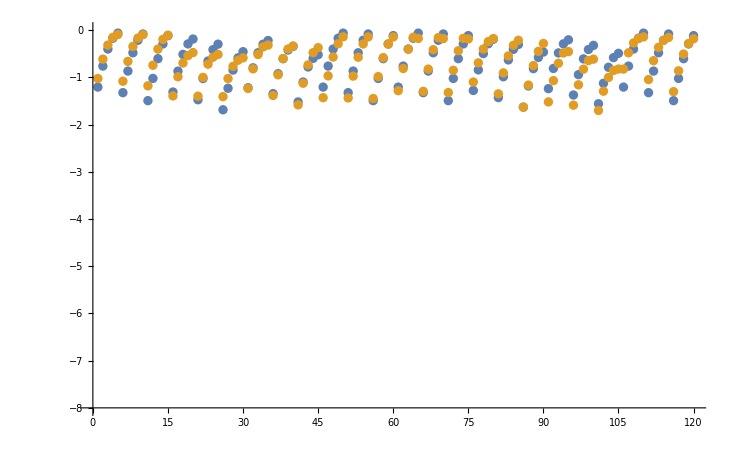

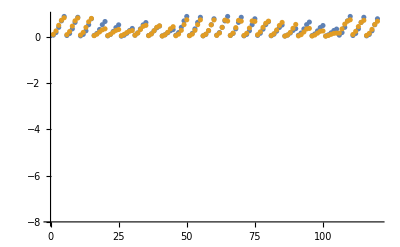

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

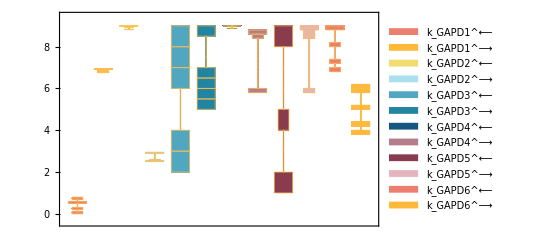

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

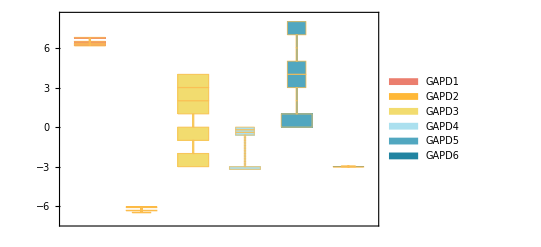

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

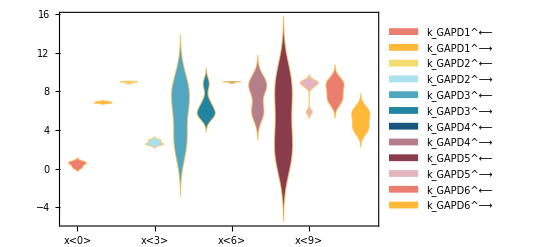

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[inputPath  <> "(.*)\\.txt"]->"$1"][[1]],{func,fittingData[[All,-2]]}];
```

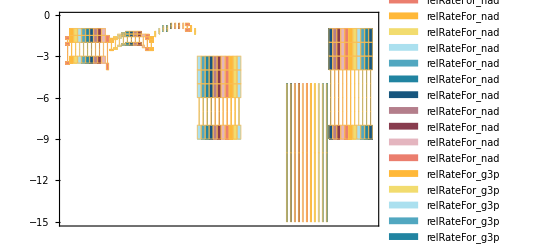

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= Underscript[E_total, Global]-> eTotal;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.46352×10^-10
0.00089 | 0.00089 | 1.3663×10^-9
0.00053 | 0.00053 | 2.89852×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268. | 268. | 8.12479×10^-10

```mathematica
backCalculateRatios[dKdRatio, dKdVal, paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 4.86486×10^-10